# Project WSS 2019 by Abraham Gadalla

# Project Calculate the volume, surface area, circumference and area of the egg shaped figure

## Surface Area and Volume of an Egg

## Write parametric equations to draw an egg shaped figure

### Drawing the egg with both Cartesian and Parametric equations

### First Using Cartesian Equations

```mathematica
ClearAll["Global`*"];Clear[a];
```

```mathematica
Manipulate[
plt1 =Plot[{Sqrt[(2 - √2)^2 a^2 - (x+ a)^2],-Sqrt[(2 - √2)^2 a^2 - (x+ a)^2]},{x,√2 a - 3 a,-√2 a},PlotStyle->{{Thick,Purple}},AxesOrigin->{0,0},Axes->True,AxesStyle->Directive[Thick,Italic,Black,14],AspectRatio->Automatic];
plt2 =Plot[{Sqrt[4 a^2 - (x)^2]-a,-Sqrt[4 a^2 - (x)^2]+a},{x,-√2 a ,0},PlotStyle->{{Thick,Pink}},AxesOrigin->{0,0},Axes->True,AspectRatio->Automatic];
plt3 =Plot[{Sqrt[ a^2 - (x)^2],-Sqrt[ a^2 - (x)^2]},{x,0 ,a},PlotStyle->{{Thick,Red}},AxesOrigin->{0,0},Axes->True,AspectRatio->Automatic];
text=Graphics[{Text[Style["y = √((2  -  SqrtBox[2])^2)",Purple,12],{(-1.5)a,0.3}],Text[Style["y = √(4 a^2  -  x^2) -a",Black,12],{(√2-3)a+1.30,1.5}],Text[Style["y = √(a^2  -  x^2)",Red,12],{0.5a,1.5}],
Text[Style["a",16,Black],{a/2,-0.4}],Text[Style["-a",16,Black],{-a/2,-0.4}],
Text[Style[TraditionalForm[{0, 0}],18,Red],{0,-0.3}],
PointSize[0.025],Point[{0,0}],Point[{-a,0}],Blue,Point[{-√2 a,0 }],Red,Point[{-3 a + √2 a,0}],Purple,Point[{-√2 a,-√2 a + a}],
Arrow[{{0,-a},{-√2 a,√2 a - a}}],Blue,Line[{{-√2 a,√2 a - a},{-√2 a,-√2 a + a}}],{Black,Arrowheads[{-0.04,0.04}],Arrow[{{0,-0.6},{a,-0.6}}],Arrow[{{0,-0.6},{-a,-0.6}}],Line[{{a,0},{a,-0.7}}],Line[{{-a,0},{-a,-0.7}}]}}];
dimensions=Graphics[{Line[{{√2 a - 3 a,0},{√2 a - 3 a,-a-0.5}}],Line[{{0,0},{0,-a-0.5}}],Line[{{-√2 a,-√2 a + a},{-√2 a,- a}}],

Arrow[{{-√2 a+0.6 ,-a+0.3},{-√2 a ,-a+0.3}}],

Arrow[{{√2 a - 3 a-0.6,-a+0.3},{√2 a - 3 a,-a+0.3}}],{Arrowheads[{-0.04,0.04}],Arrow[{{0,-a-0.4},{√2 a - 3 a,-a-0.4}}],

Text[Style["|4 a-2√2a| ",16,Black],{-1.7a ,-a+0.5}],


Text[Style["| 3 a - √2a |",16,Black],{-a,-a-0.2}]}}];
If[showdim,Show[plt1,plt2,plt3,text,dimensions,ImageSize->Large,PlotRange->All],Show[plt1,plt2,plt3,text,ImageSize->Medium,PlotRange->All]
],
Row[{
Control[{{a,2,"radius"},1,5,Appearance->"Labeled"}],Spacer[15],Control[{{showdim,True,"show\ndimension"},{False,True}}]}],TrackedSymbols:>{a,showdim}]
```

## Calculate the area and the circumference of an egg-shaped figure.

```mathematica
Manipulate[
Clear [c1,c2,c3,c4,area,circom];
c1:={Thick, Purple, Circle[{0,0},a,{-π/2,π/2}],Point[{0,0}]};
c2:={Thick, Pink, Circle[{0,a},2a,{5π/4,3π/2}]};
c3:={Thick, Pink, Circle[{0,-a},2a,{π/2,3π/4}]};
c4:={Thick, Red, Circle[{-a,0},(2-√2)a,{3π/4,5π/4}],Point[{-a,0}]};
l1:={Purple, Line[{{0,-a},{0,a}}]};
l2:={Blue, Line[{{-a √2,a- a √2},{0,a}}]};
l3:={Orange, Line[{{-a √2,-a+ a √2},{0,-a}}]};
l4:={Black, Line[{{-3 a+a √2,0},{a,0}}]};
t1:=Text[Style["a",{"Times-Bold",24}],{a/2,-0.1}];
t2:=Text[Style["a",{"Times-Bold",24}],{-a/2,-0.1}];
quetn:=Text[Style["Prove that the area of the figure = ( ( 3 - √2 ) π - 1) a^2  \nand the circumference of the figure  = ( 3 - (√2)/2 ) (π a)",18, Bold, Purple],{-1,3}];
area:=Text[Style[Row[{"Area of the figure = ",NumberForm[( (3 - √2)π-1) a^2,{3,2}],"\n\n"}],18,Blue,Bold],{-2,3}];
circom:=Text[Style[Row[{"Circumference = ",NumberForm[( 3-(√2)/2) π a,{3,2}],"\n\n"}],18,Bold,Purple],{-2,2.5}];
If[Answer,Show[Graphics[{c1,c2,c3,c4,t1,t2,l1,l2,l3,l4,area,circom},Axes->False,AxesOrigin->{0,0},Axes->False,ImageSize->Large]],
Show[Graphics[{c1,c2,c3,c4,t1,t2,l1,l2,l3,l4,quetn},Axes->False,AxesOrigin->{0,0},AspectRatio->Automatic,ImageSize->Large]]],
Row[{Control[{{a,2.,"Radius a"},1,5,Appearance->"Labeled"}],Spacer[45],Control[{{Answer,False,"Answer"},{False,True}}]}],TrackedSymbols->{a,Answer},SaveDefinitions->True]
```

The egg - shaped figure is drawn using a Piecewise Function as follows :

1. A semicircle with radius = "a"  , center at origin and angle between -π/2, π/2.

2. A sector with radius = 2 a , center at {0, - a) and angle between π/2 and 3π/4.

3. A sector with radius = 2 a - a √2 , center at {-a, 0) and angle between3 π/4 and 5 π/4.

4. A sector with radius = 2 a , center at {0,  a) and angle between 5π/4 and 3π/2.

The students are asked to write the parametric equations of the egg-shaped figure, calculate its circumference and its area.

Calculus students are asked to calculate the volume and the surface area of the figure based on the assigned value of the main radius a.

The circumference of the figure = (3 - √2/2) π a  cm, which is approximately = 2.293 π a cm.

The circumference is calculated as follows : Twice the upper curve = 
 2  { quarter circle with radius  a + Arc of a sector whose radius = 2 a  + 
 Arc of a sector with radius (2 - √2 ) a }

Circumference of the egg-shaped figure =

2( (π a)/2 + 1/4 π (2 a) +π/4 ( 2 - √2) a )= (3 -(√2)/2) π a cm.

```mathematica
FullSimplify[ 2( (π a)/2 + 1/4 π (2 a) +π/4 ( 2 - √2) a )]
```

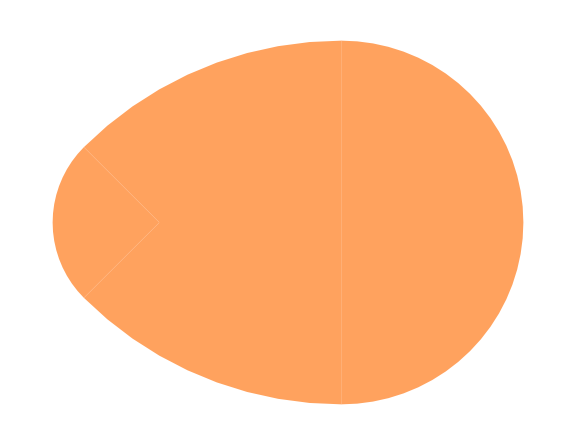

```mathematica
a:=2;
Clear [c1,c2,c3,c4,area,circom];
c1:={ColorData["BlackBodySpectrum",1000 4],Disk[{0,0},a,{-π/2,π/2}]};
c2:={ColorData["BlackBodySpectrum",1000 4], Disk[{0,a},2a,{5π/4,3π/2}]};
c3:={ColorData["BlackBodySpectrum",1000 4],Disk[{0,-a},2a,{π/2,3π/4}]};
c4:={ColorData["BlackBodySpectrum",1000 4],Disk[{-a,0},(2-√2)a,{3π/4,5π/4}]};
txt:=Graphics[Text@Style["Happy Easter",42,Italic,Purple]];
txtg:=Graphics[Text@Style["Frohe Ostern",42,Italic,Purple]];
egg=Graphics[{c1,c2,c3,c4},ImageSize->Large,AspectRatio->Automatic]
eggt:=Graphics[Table[Translate[#,6(1+GoldenRatio){GoldenRatio Cos[k π/6],Sin[k π/6]}],{k,1,12,1}]&/@egg];
(*Show[txtg,eggt,PlotRange->Automatic]
Show[txt,eggt,PlotRange->Automatic]*)
```

## Project Calculate the volume, surface area, circumference and area of the egg shaped figure

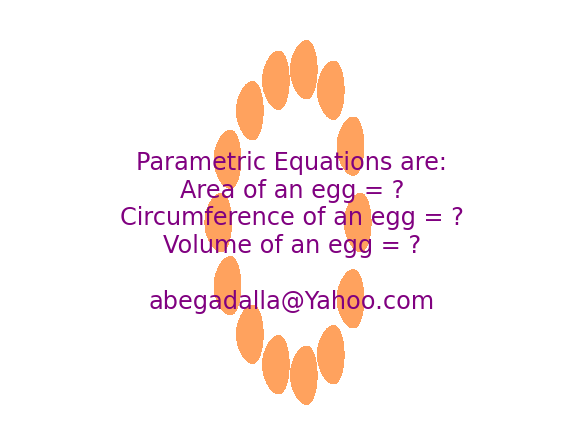

```mathematica
a:=6;
Clear [c1,c2,c3,c4,area,circom];
c1:={ColorData["BlackBodySpectrum",1000 4],Disk[{0,0},a,{-π/2,π/2}]};
c2:={ColorData["BlackBodySpectrum",1000 4], Disk[{0,a},2a,{5π/4,3π/2}]};
c3:={ColorData["BlackBodySpectrum",1000 4],Disk[{0,-a},2a,{π/2,3π/4}]};
c4:={ColorData["BlackBodySpectrum",1000 4],Disk[{-a,0},(2-√2)a,{3π/4,5π/4}]};
txt:=Graphics[Text[Style["Happy Easter",32,Italic,Purple],{-6.75,0}]];
txtg:=Graphics[Text@Style["Frohe Ostern",32,Italic,Purple]];
txtm:=Graphics[Text[Style["Parametric Equations are:\nArea of an egg = ?\nCircumference of an egg = ?\nVolume of an egg = ?\n\nabegadalla@Yahoo.com",24,Italic,Purple],{-8.75,-2}]];
txts:=Graphics[Text[Style["Sayed Gadalla",32,Italic,Purple],{-6.75,0}]];
egg:=Graphics[{c1,c2,c3,c4},ImageSize->Large,AspectRatio->Automatic];
eggt1:=Graphics[Table[Translate[#,12(1+GoldenRatio){ Cos[k π/12],Sin[k π/12]}],{k,-6,6,2}]&/@egg];
eggt2:=Graphics[Table[Translate[#,24(1+GoldenRatio){ Cos[k π/12], Sin[k π/12]-0.5}],{k,7.,9,1}]&/@egg[[1]]];
eggt3:=Graphics[Table[Translate[#,24(1+GoldenRatio){ Cos[k π/12],0.5+Sin[k π/12]}],{k,15,17,1}]&/@egg[[1]]];
eggt4:=Graphics[Table[Translate[#,12 (2-√2)(1+GoldenRatio){-1/(2-√2)+ Cos[k π/12],Sin[k π/12]}],{k,9,15,3}]&/@egg[[1]]];
sh1:=Show[txtm,eggt1,PlotRange->Automatic];
sh2:=Show[eggt2,PlotRange->Automatic];
sh3:=Show[eggt3,PlotRange->Automatic];
sh4:=Show[eggt4,PlotRange->Automatic];
Show[sh1,sh2,sh3,sh4,ImageSize->Large,PlotRange->Automatic]
```

## Putting the previous pieces together

## Project Calculate the volume, surface area, circumference and area of the egg shaped figure

```mathematica
ClearAll["Global`*"];
```

```mathematica
DynamicModule[{a,equations,vol,areaegg,surfArea,circumf},Manipulate[
Column[{
Item[

Column[{If[equations,Style[Row[{Style[" 1) The Parametric Equations are: \n",Italic],Style["x = "],Style[a ],Style[" Cos [ t ],   y =  "],Style[a],Style[" Sin [ t ],         - π/2 ≤ t ≤ π/2 \n"],Style["x = "],Style[2 a ],Style[" Cos [ t ],   y =  "],Style[-a],Style[" + "],Style[ 2 a ],Style[" Sin [ t ],     π/2 ≤ t ≤ (3  π)/4 \n"],
Style["x = "],Style[a (2 - √2 )],Style[" Cos [ t ] - "], Style[a],Style [" ,  y =  "],Style[a (2 - √2)],Style[" Sin [ t ],   (3  π)/4 ≤ t ≤ (5  π)/4 \n"],
Style["x = "],Style[2 a ],Style[" Cos [ t ] "], Style [",   y =  "],Style[a],Style["  +  "], Style[2 a ],Style[" Sin [ t ],    (5  π)/4 ≤ t ≤ (3  π)/2 "]}],15,Purple],
Text@Style[" 1) Write the parametric equations for the egg according to the figure",14,Black,Italic]],
(*The circumference of the egg  = ( 3 - (√2)/2 ) (π a) *)
Row[{If[circumf,Style[Row[{" 2)  Circumference = ",NumberForm[( 3-(√2)/2) π a,{5,3}]," cm"}],14,Blue,Italic],
Text@Style[" 2) Calculate the circumsference of the egg",14, Black,Italic]],Spacer[5],
(* Area of the egg = ( ( 3 - √2 ) π - 1) a^2  *)
If[areaegg,Style[Row[{"       3)  Area of the egg = ",NumberForm[( (3 - √2)π-1) a^2,{5,3}]," cm^2"}],14,Blue,Italic],
Text@Style[" 3) Calculate the area of the egg",14, Black,Italic]],If[vol,Style[Row[{"4) Volume of the Egg = ",NumberForm[-π (40. √2 +3 π -71) a^3 /3,{6,3}]," cm^3 "}],14,Blue,Italic],
Text@Style["4) Calculate the volume of the egg",14,Italic]],Spacer[10],
(* Surface Area  = (14 -4 √2-π) a^2*)
If[surfArea,Style[Row[{"5)  Surface Area = ",NumberForm[ (14 -4 √2-π) a^2,{5,3}]," cm^2"}],14,Blue,Italic],
Text@Style["5) Calculate the surface area of the egg",14, Black,Italic]]}]
}  ],Alignment->{Center},Frame->All],
Item[

(* Drawing the three dimensions egg *)

pv1=RevolutionPlot3D[{Sqrt[a^2 - x^2]},{x,0,a},RevolutionAxis->{1,0,0},Boxed->False,Mesh->False,Axes->None,ColorFunction->Function[{Opacity[0.3],Hue[6]}]];
pv2=RevolutionPlot3D[{ -a + Sqrt[4 a^2 - x^2]},{x,-√2 a,0},RevolutionAxis->{1,0,0},Boxed->False,Mesh->False,Axes->None,ColorFunction->Function[{Opacity[0.3],Hue[6]}]];
pv3=RevolutionPlot3D[{Sqrt[(2 a - a Sqrt[2])^2 - (x + a )^2]},{x,-3 a+a √2,-√2 a},RevolutionAxis->{1,0,0},Boxed->False,Mesh->False,Axes->None,ColorFunction->Function[{Opacity[0.3],Hue[6]}]];

egg:=Graphics[{d1,d2,d3,d4},ImageSize->Large,AspectRatio->Automatic];
eggt1:=Graphics[Table[Translate[#,2 a(1+GoldenRatio){ Cos[k π/12],Sin[k π/12]}],{k,-6,6,2}]&/@egg];
eggt2:=Graphics[Table[Translate[#,4 a(1+GoldenRatio){ Cos[k π/12], Sin[k π/12]-0.5}],{k,7.,9,1}]&/@egg[[1]]];
eggt3:=Graphics[Table[Translate[#,4 a(1+GoldenRatio){ Cos[k π/12],0.5+Sin[k π/12]}],{k,15,17,1}]&/@egg[[1]]];
eggt4:=Graphics[Table[Translate[#,2 a (2-√2)(1+GoldenRatio){-1/(2-√2)+ Cos[k π/12],Sin[k π/12]}],{k,9,15,3}]&/@egg[[1]]];
sh1:=Show[txt,eggt1,PlotRange->Automatic];
sh2:=Show[eggt2,PlotRange->Automatic];
sh3:=Show[eggt3,PlotRange->Automatic];
sh4:=Show[eggt4,PlotRange->Automatic];

Grid[{{Show[pv1,pv2,pv3,ImageSize->Small,PlotRange->All],
Show[Graphics[{c1,c2,c3,c4,t1,t2,l1,l2,l3,l4,dimension},Axes->False,AxesOrigin->{0,0},AspectRatio->Automatic,ImageSize->250]]},{Show[sh1,sh2,sh3,sh4,ImageSize->Small,PlotRange->Automatic]}}],Alignment->{Left},Frame->All]
}],
Row[{Control[{{a,2.," a"},1.,4.,ImageSize->Tiny,Appearance->"Labeled"}],Control[{{equations,True,"Param. eqns"},{False,True}}],Spacer[3],Control[{{circumf,False,"circumf."},{False,True}}], Spacer[3], Control[{{areaegg,False,"area"},{False,True}}],Spacer[3],  Control[{{vol,False,"Volume"},{False,True}}],Spacer[3],
Control[{{surfArea,False,"Surf. Area"},{False,True}}]
}],Initialization:>{Clear [c1,c2,c3,c4,area,circom];
c1:={Thick, Purple, Circle[{0,0},a,{-π/2,π/2}],Point[{0,0}]};
c2:={Thick, Pink, Circle[{0,a},2a,{5π/4,3π/2}]};
c3:={Thick, Pink, Circle[{0,-a},2a,{π/2,3π/4}]};
c4:={Thick, Red, Circle[{-a,0},(2-√2)a,{3π/4,5π/4}],Point[{-a,0}]};
l1:={Purple, Line[{{0,-a},{0,a}}]};
l2:={Blue, Line[{{-a √2,a- a √2},{0,a}}]};
l3:={Orange, Line[{{-a √2,-a+ a √2},{0,-a}}]};
l4:={Black, Line[{{-3 a+a √2,0},{a,0}}]};
dimension:={Black,Line[{{-a,0},{-a,-0.72}}],Arrowheads[{-0.05,0.05}],Arrow[{{0,-0.55},{-a,-0.55}}]};
t1:=Text[Style["a",{"Times-Bold",14}],{a/2,-0.4}];
t2:=Text[Style[Row[{Style["a = "],Style[NumberForm[a,{3,2}]],Style[" cm "]}],{"Times-Bold",14}],{-a/2,-0.4}];
d1:={FaceForm[Pink],Disk[{0,0},a,{-π/2,π/2}]};
d2:={FaceForm[Pink],Disk[{0,-a},2a,{π/2,3π/4}]};
d3:={FaceForm[Pink], Disk[{0,a},2a,{5π/4,3π/2}]};
d4:={FaceForm[Pink],Disk[{-a,0},(2-√2)a,{3π/4,5π/4}]};
txt:=Graphics[Text[Style["Happy Day",16,Italic,Purple],{-a+0.75,0}]];
v1=Integrate[π (a^2 - x^2),{x,0,a}];
v2=Integrate[π ( -a + Sqrt[4 a^2 - x^2])^2,{x,-√2 a,0}];
v3=Integrate[π ( (2 a - a Sqrt[2])^2 - (x + a )^2),{x,-3 a+a √2,-√2 a}];
volume := FullSimplify[v1+v2+v3];

 },TrackedSymbols->{a,equations,vol,areaegg,surfArea,circumf}]]
```